Note: This Notebook requires download of the Wolfram Quantum Frame work (see https://www.wolfram.com/quantum-computation-framework/index.php.en )

# Why Superposition ?

```mathematica
ClearAll["Global`*"]
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

```mathematica
ket0=QuantumState[{1,0}];
ket1=QuantumState[{0,1}];
u2[θ_]=N[{{Cos[θ],Sin[θ]},{Sin[θ],-Cos[θ]}}];
gate0=QuantumOperator[{{1,0},{0,1}}];
gate1=QuantumOperator[u2[Pi/2]];
gate2=QuantumOperator[u2[Pi/2+0.15]];
gate3=QuantumOperator["H"];
m1=QuantumMeasurementOperator[];
```

Above we defined a set of one qubit gates, that we labeled gate0,gate1,gate2,gate3. Our goal is to run these gates in a simple circuit shown in the diagram below.

QuantumCircuitOperator[…]

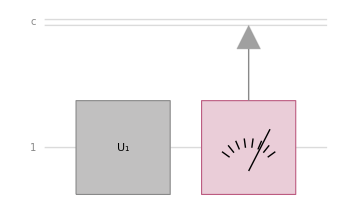

```mathematica
circuit=QuantumCircuitOperator[{gate0}]
circuitdiagram=QuantumCircuitOperator[{gate0,m1}];
circuitdiagram["Diagram"]
```

Here we consider the circuit containing “gate0” defined above.
In this diagram, the input lead to the left of the box labeled U_1  (“gate0”) represents one of the states |0⟩ or |1⟩. The box containing the meter is a measurement gate. Its output can only display one of the binary values 0 or 1. Values indicated by the meter is probabilistically determined by the output quantum state from gate U_1 and the Born rule. We will uncover the properties of gate U_1 by feeding states |0⟩ or |1⟩ into it and analyzing output statistics of the measurement gate. In the first run we are using the gate labeled “gate0”.

Let’s run the above computation several times and take statistics of output values.

Input state   1

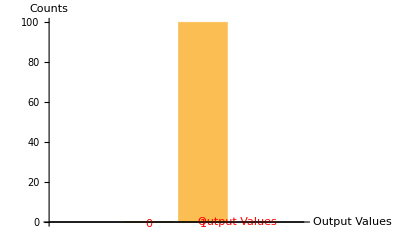

```mathematica
inputstate=ket1;
Print["Input state   ",inputstate["Formula"]]
runs=100;
qm=QuantumMeasurementSimulation[circuit[inputstate],QuantumMeasurementOperator /@{"Z"},runs];
BarChart[qm[[1]],ChartLabels->{"0","1"},AxesLabel->{"Output Values","Counts"},LabelStyle->{Red,Bold}]
```

In the run executed above, we fed state | 1 ⟩ into U_1 100 times. The graph shows that the measurement device registered the value 1 for each run.  

Exercise: Repeat this circuit run but let |0⟩ be the input state by replacing command “inputstate=ket1”  above with “inputstate=ket0”  

Analysis: You should have counted 100 instances of the value “0” in this exercise. Convince yourself  that “gate0” represents an Identity gate; that is it does not alter the input state.

We now repeat this circuit using “gate1”.

```mathematica
circuit=QuantumCircuitOperator[{gate1}];
circuitdiagram=QuantumCircuitOperator[{gate1,m1}];
circuitdiagram["Diagram"]
```

-Graphics-

Let’s run the above computation several times and take statistics of output values.

Input state   1

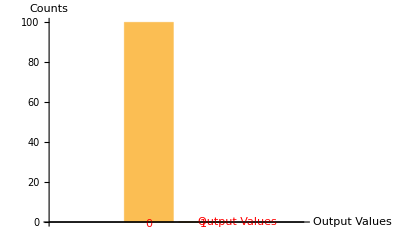

```mathematica
runs=100;
inputstate=ket1;
Print["Input state   ",inputstate["Formula"]]
qm=QuantumMeasurementSimulation[circuit[inputstate],QuantumMeasurementOperator /@{"Z"},runs];
BarChart[qm[[1]],ChartLabels->{"0","1"},AxesLabel->{"Output Values","Counts"},LabelStyle->{Red,Bold}]
```

In the run executed above, we fed state | 1 ⟩ into U_1 100 times, the graph shows that the measurement device counted the value 0 for each run.  

Exercise: Repeat this circuit run but let |0⟩ be the input state by replacing command “inputstate=ket1”  above with “inputstate=ket0”  

Analysis: You should have counted 100 instances of the value “1” in the above exercise: convince yourself from these statistics that “gate0” represents a NOT gate; that is “flips” the value of “0” into “1” and vice versa.

Now we repeat with a new gate “gate2”

```mathematica
circuit=QuantumCircuitOperator[{gate2}];
circuitdiagram=QuantumCircuitOperator[{gate2,m1}];
circuitdiagram["Diagram"]
```

-Graphics-

Let’s run the above computation several times and take statistics of output values.

Input state   1

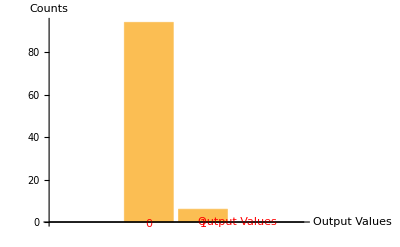

```mathematica
runs=100;
inputstate=ket1;
Print["Input state   ",inputstate["Formula"]]
qm=QuantumMeasurementSimulation[circuit[inputstate],QuantumMeasurementOperator /@{"Z"},runs];
BarChart[qm[[1]],ChartLabels->{"0","1"},AxesLabel->{"Output Values","Counts"},LabelStyle->{Red,Bold}]
```

In the run executed above, we fed state | 1 ⟩ into U_1 100 times, the graph shows that the measurement device counted mostly the value “0” for the runs, but some runs gave the value “1”  

Exercise: Repeat this circuit run but let |0⟩ be the input state by replacing command “inputstate=ket1”  above with “inputstate=ket0”  

Analysis: You should have mostly counted instances of the value “1” in the above exercise, but did find instances where the value “0” was recorded: convince yourself from these statistics that “gate2” represents a “noisy” NOT gate; that is it mostly “flips” the value of “0” into “1” and vice versa, but sometimes acts, because of imperfections, as an identity gate. Noise is a feature in all real-life gates; though it can be managed using so-called error-correction codes (see Chap9 in text)

Lets try to figure out what “gate3” is doing

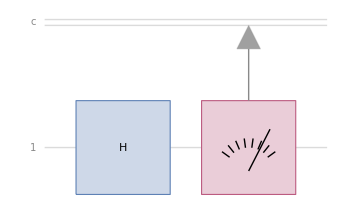

```mathematica
circuit=QuantumCircuitOperator[{gate3}];
circuitdiagram=QuantumCircuitOperator[{gate3,m1}];
circuitdiagram["Diagram"]
```

Let’s run the above computation several times and take statistics of output values.

Input state   0

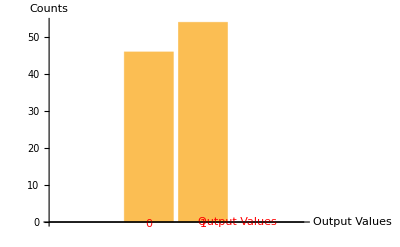

```mathematica
runs=100;
inputstate=ket0;
Print["Input state   ",inputstate["Formula"]]
qm=QuantumMeasurementSimulation[circuit[inputstate],QuantumMeasurementOperator /@{"Z"},runs];
BarChart[qm[[1]],ChartLabels->{"0","1"},AxesLabel->{"Output Values","Counts"},LabelStyle->{Red,Bold}]
```

In the run executed above, we fed state | 0⟩ into U_1 100 times, the graph shows that the measurement device counted the value “0” for roughly 1/2 of the runs, but gave the value “1”, for the remaining runs.  

Exercise: Repeat this circuit run but let |1⟩ be the input state by replacing command “inputstate=ket1”  above with “inputstate=ket0”  

Analysis: from these statistics we could infer that “gate3” is either a very noisy NOT, or Identity gate. You could simulate such a gate yourself at home. Take a coin initially with the “head” state showing.  Flip your coin and register 
the face of the coin when landed. You should get similar statistics to that obtained using “gate3”. 

Based on our experiments let’s call “gate3” a “ Coin flip gate”, as it demonstrates similar statistics. To check if that is the case. Perform another experiment at home, flip a coin once and use that output to flip the coin again. What type of statistics  do you observe after two consecutive flips ?  Convince yourself that you arrive at the same statistics as obtained in a single flip experiment.

If our interpretation is correct let’s perform the quantum simulation shown by the circuit diagram below. It involves two consecutive actions of “gate3”. That is the output of the first traversal through “gate3” is used as input to an additional  “gate3”.

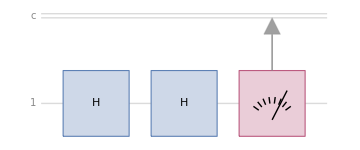

```mathematica
circuit=QuantumCircuitOperator[{gate3,gate3}];
circuitdiagram=QuantumCircuitOperator[{gate3,gate3,m1}];
circuitdiagram["Diagram"]
```

Let’s run the above computation several times and take statistics of output values.

```mathematica
runs=100;
inputstate=ket0;
Print["Input state   ",inputstate["Formula"]]
qm=QuantumMeasurementSimulation[circuit[inputstate],QuantumMeasurementOperator /@{"Z"},runs];
BarChart[qm[[1]],ChartLabels->{"0","1"},AxesLabel->{"Output Values","Counts"},LabelStyle->{Red,Bold}]
```

Input state   0

-Graphics-

Note the counterintuitive result that with two quantum “coin-flip” gates the system returns to its initial state |0⟩. Try repeating this experiment starting with input state |1 ⟩. Show that a measurement reveals the value “1” after transversal through the circuit.

Exercise: run the circuit below. What are your predictions for the measurement gates as shown. How do you reconcile the results obtained in the previous circuit with the “coin-flip” analogy ?  Can you predict the action of “gate3” on states |0⟩ and |1⟩, that explain these statistics ?

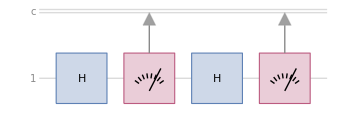

```mathematica
circuit=QuantumCircuitOperator[{gate3,m1,gate3}];
circuitdiagram=QuantumCircuitOperator[{gate3,m1,gate3,m1}];
circuitdiagram["Diagram"]
```

Answer: We can reconcile the above observation that “gate3”, which we call the “H” or Hadamard Gate (see Chap3 in text) has the following properties

H |0⟩ = 1/(√2) (|0⟩ + |1 ⟩)      H|1⟩ = 1/(√2) (|0⟩ - |1 ⟩) 

That is, the gate acting on the state |0⟩ and |1⟩ as above, create “superposition states”.